```mathematica
<<Eidomatica`
```

Some examples for optical flow computation and visualization:

```mathematica
(*pixel*)
reference=Image@{{1,0,0,0},{0,0,0,0},{0,0,0,0}}
sample=Image@{{0,0,0,0},{0,0,1,0},{0,0,0,0}}
```

```mathematica
(*cell images*)
reference=-Graphics-;
```

```mathematica
sample=-Graphics-;
```

```mathematica
(*rectangle*)
reference=ColorConvert[GaussianFilter[Image@Show[{Graphics[Raster@Table[0,{40},{50}]],Graphics[{White,Rectangle[{5,5},{20,15}]}]},ImagePadding->0,PlotRangePadding->0,ImageSize->20],4],"Grayscale"]
sample=ColorConvert[GaussianFilter[Image@Show[{Graphics[Raster@Table[0,{40},{50}]],Graphics[{White,Rectangle[{30,25},{45,35}]}]},ImagePadding->0,PlotRangePadding->0,ImageSize->20],4],"Grayscale"]
```

-Graphics-

-Graphics-

```mathematica
reference=ColorConvert[Image@Show[{Graphics[Raster@Table[0,{40},{50}]],Graphics[{White,Rectangle[{5,5},{20,15}]}]},ImagePadding->0,PlotRangePadding->0,ImageSize->50],"Grayscale"]
sample=ColorConvert[Image@Show[{Graphics[Raster@Table[0,{40},{50}]],Graphics[{White,Rectangle[{30,25},{45,35}]}]},ImagePadding->0,PlotRangePadding->0,ImageSize->50],"Grayscale"]
```

-Graphics-

-Graphics-

```mathematica
vf=eOpticalFlow[reference,sample,Lambda->50,Iterations->1,Omega->80,Radius->50,ReturnAll->False];
```

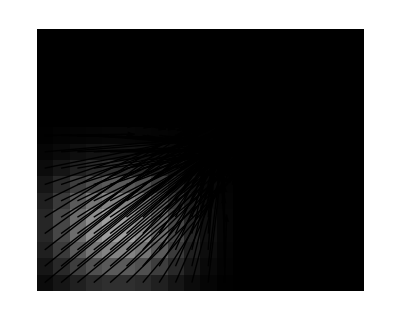

```mathematica
eVectorFieldPlot[vf,reference,VisualizationStyle->"Arrow"]
```

```mathematica
eVectorFieldPlot[vf,VisualizationStyle->"Plain",ShowColorWheel->True]
```

{-Graphics-,-Graphics-}

```mathematica
eVectorFieldPlot[vf,VisualizationStyle->"Angle",ShowColorWheel->True]
```

{-Graphics-,-Graphics-}

```mathematica
eVectorFieldPlot[vf,VisualizationStyle->"Surface",ShowColorWheel->True]
```